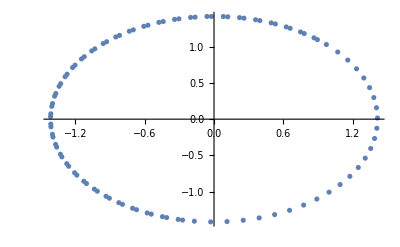

```mathematica
sys:={Subscript[x, 1][n + 1]- (0.995+a) Subscript[x, 1][n] + 0.1 Subscript[x, 2][n] == 0, Subscript[x, 2][n + 1]- 0.1 Subscript[x, 1][n] - (0.995+b) Subscript[x, 2][n] == 0,Subscript[x, 1][0]==Subscript[x, 10],Subscript[x, 2][0]==Subscript[x, 20]}

Subscript[x, 10]=1;
Subscript[x, 20]=1;


a=0;
b=0;
sol=RSolveValue[sys, {Subscript[x, 1][n],Subscript[x, 2][n]}, {n}];
m1[n_]=sol[[1]];
m2[n_]=sol[[2]];
plot1=ListPlot[Table[{m1[i], m2[i]}, {i, 100}]];


Manipulate[
sol4=RSolveValue[sys, {Subscript[x, 1][n],Subscript[x, 2][n]}, {n}];
m14[n_]=sol[[1]];
m24[n_]=sol[[2]];
plot1=ListPlot[Table[{m14[i], m24[i]}, {i, it}],PlotRange->Automatic], 
{it, 1, 100}]




a=0;
b=0;
sol=RSolveValue[sys, {Subscript[x, 1][n],Subscript[x, 2][n]}, {n}];
m1[n_]=sol[[1]];
m2[n_]=sol[[2]];
plot1=ListPlot[Table[{m1[i], m2[i]}, {i, 100}]];
```